# Pieces of Art Appreciated with Wolfram Language Machine Learning

Applying machine learning and the Wolfram Language functionality to learn about five of the most famous painting artist in history.

Diego Gutierrez Coronel, Jun. 28,  2018

Mathematica and the Wolfram Language is known for being a symbolic language that also works well for plotting and visualisation. However it can be used for much more, with a simple but broad functionality for Machine Learning. It can be very useful to analyze data, simulate processes, either scientific or mathematical, and even develop software for different applications. Art appreciation and categorization can be though of as a subjective topic not related with computation. However, nowadays the tools developed by machine learning have already been used to study art history, style, among others.

## From Renaissance to Post-Impressionism

We will apply some of the Machine Learning tools in the Wolfram Language to look at five different artist as shown in the list created below. Each one of the artists belonging to different periods of time and stylistic movements in art. Representing the Italian Renaissance is Sandro Botticelli, form the Baroque period is Spanish artist Diego Velázquez, and his famous compatriot Pablo Picasso, figure of the Cubistic style. Additionally we have Claude Monet and Vincent van Gogh from opposing movements, Impressionism and Post-Impressionism, respectively. With the Wolfram Language, this set of strings can be converted into real-world entities that can be used symbolically.

```mathematica
paintersList = {"Sandro Boticelli", "Diego Velazquez", "Claude Monet", "Vincent Van Gogh", "Picasso"};
Interpreter["Person"][#] & /@ paintersList
```

{Sandro Botticelli,Diego Velázquez,Claude Monet,Vincent van Gogh,Pablo Picasso}

These entities contain different properties and thus we can access information and various types of data from this symbolic expressions. Here we take a random sample of three famous paintings from Boticelli. We can also check the number of “Notable Artworks” Images stored under Boticelli’s Entity.

```mathematica
EntityValue[RandomSample[LinguisticAssistant["NotableArtworks"], 3], "Image"]
Length[Cases[EntityValue[EntityList[LinguisticAssistant["NotableArtworks"]],"Image"],_Image]]
```

{-Graphics-,-Graphics-,-Graphics-}

52

With the following code we assign a list of 5 lists of notable paintings from each of the artists presented.

```mathematica
paintingImages=Cases[EntityValue[
RandomSample[Interpreter["Person"][#]["NotableArtworks"], 40]
,"Image"]
,_Image]&/@paintersList;
```

We can also see the total number of paintings stored below and a sample of these.

```mathematica
Length[Flatten[paintingImages]]
paintingImages⟦4,9⟧
```

177

-Graphics-

## Color Appreciation

These paintings could be analyzed in different ways. We could for example see the distinctive colors used by each artist by taking the pixel color of all images for each of the artist and plotting it in a Chromaticity Plot.

```mathematica
colors={Blue,Red,Green,Gray,Orange};
Legended[
	Show[
		ChromaticityPlot[#1,PlotStyle->#2,Appearance-> "VisibleSpectrum"]&@@@Transpose[{paintingImages,colors}]
		(*Table[ChromaticityPlot[paintingImages[[i]],PlotStyle->colors[[i]],Appearance-> "VisibleSpectrum"],{i,1,5}]*)
	],
	SwatchLegend[colors,paintersList]]
```

-Graphics-

This same data set can be visualized thoroughly and interactively by plotting it in three dimensions. The description box in light blue is just a set of options for plotting so do not focus too much on those.

```mathematica
Iconize[PlotStyle->Opacity[0.2],Appearance-> "VisibleSpectrum"]
```

```mathematica
Legended[
Show[
Table[ChromaticityPlot3D[paintingImages[[i]],PlotStyle->colors[[i]],],{i,1,5}]],
SwatchLegend[colors,paintersList]]
```

-Graphics3D-

It can be seen that the colors used by all artist are clustered in a relatively small range, however each one of them seems to disperse in different directions in the cluster. For instance Van Gogh does not use so many light colors as Monet or Picasso.

## Introduction Machine Learning

For now we will generate a list of rules that connects painters with their paintings as seen in a random sample below.

```mathematica
dataset=Thread/@Thread[paintingImages->paintersList];
dataset=RandomSample[Flatten[dataset]];
RandomSample[dataset,5]
```

{-Graphics-→Vincent Van Gogh,-Graphics-→Claude Monet,-Graphics-→Claude Monet,-Graphics-→Vincent Van Gogh,-Graphics-→Sandro Boticelli}

Now we will look at different two paradigms in machine learning implemented in Wolfram Language Functions. These are supervised and unsupervised learning. In a general and conceptual way:

Supervised learning: takes a relation between inputs and outputs.

Unsupervised learning: takes only outputs and finds patterns or clusters.

We separate the total number of paintings in a training set and a test set in order to work with built-in functions.

```mathematica
Length[dataset]
trainingset=dataset[[1;;140]];
testset=dataset[[141;;]];
```

177

## Classifying by Artist

Below we use the built-in function Classify to generate a classifier function using the training set defined before. This employs the best model to be able to classify paintings with an intrinsic probability, and some general features useful for testing it. It can be seen, that by clicking in the plus sign of the description the classifier function used either a Logistic Regression or Nearest Neighbors method.

```mathematica
cfunction=Classify[trainingset]
```

ClassifierFunction[…]

Now the classifier function is used on a test set, and then see the interesting and quantitative results from the test.

```mathematica
cmeasurements=ClassifierMeasurements[cfunction,testset]
```

ClassifierMeasurementsObject[…]

With the following it can be seen how accurate is the classifier function. Also a confusion matrix can show the performance of the classifier function for the different elements in the training set.

0.649±0.08

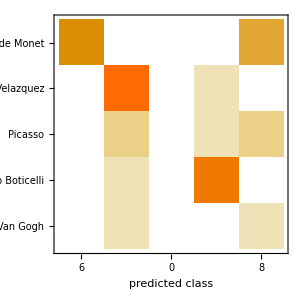

```mathematica
cmeasurements["Accuracy","Uncertainty"-> True]
cmeasurements["ConfusionMatrixPlot"]
```

It can be seen that the classifier confuses Vincent Van Gogh with Claude Monet, the most closely related styles from the five presented, even though Post-Impressionism was a reaction to it’s predecessor movement, specially regarding the use of light an color in natural environments. The classifier and machine learning algorithms does not know this, but it may associate some of the recursive themes in both movements.

If we used the classifier function with van Gogh’s “The Yellow House” we would probably see Van Gogh and Claude Monet as the two most probable ones.

```mathematica
ReverseSort@cfunction[-Graphics-,"Probabilities"]
```

<|Claude Monet→0.485714,Vincent Van Gogh→0.393432,Sandro Boticelli→0.105419,Diego Velazquez→0.00985222,Picasso→0.00558292|>

We could apply the classifier function to any painting or image that is not in the training set. For instance classifying a picture of myself would result in the classification that associates to either Van Gogh, Diego Velazquez or Picasso. In my defense , given I may not look like the distorted and abstract figures Picasso painted, this classification could be due to the mix of color of the image, which would be more closely related to these painters artwork.

```mathematica
ReverseSort@cfunction[-Graphics-,"Probabilities"]
```

<|Diego Velazquez→0.390805,Vincent Van Gogh→0.298194,Sandro Boticelli→0.105419,Claude Monet→0.104762,Picasso→0.100821|>

## Feature Extraction and Space Plot

Built-in functions that relate more to unsupervised learning can be used to see how paintings are separated depending on features extracted by different algorithms. For instance one could extract different features from a training set represented as a vector or finite list of values.

```mathematica
fextraction=FeatureExtraction[Keys@trainingset]
```

FeatureExtractorFunction[…]

Now we can apply this function to an image from the same set and see how the function generates a set of values in a large vector or list.

```mathematica
Keys@trainingset[[2]]
fextraction[%]
```

-Graphics-

{1.64857,-0.407447,0.299479,-1.49142,0.522498,-0.0744475,-0.831387,-0.711773,0.468599,-0.4606,-0.34797,1.32775,1.04189,-0.662117,-0.933501,0.0293495,-0.165943,-0.490848,-1.12996,-0.191858,0.953129,0.541712,0.063478,1.05015,-0.51968,-0.136935,0.699211,-0.807784,-0.0693278,1.8874,0.853252,-0.100689,0.979596,0.452472,0.604107,0.957553,0.413448,0.784579,-0.761359,-0.150047,-0.884172,0.0739785,-0.29882,-0.791743,1.74289,-0.85083,0.833584,1.23594,2.17517,0.071381,2.63408,-0.073276,0.0348249,1.78686,1.31502,0.353489,-0.369022,1.45531,-0.195205,-0.575291,-0.48378,0.0561436,1.02012,3.01518,-0.806997,-0.318583,-0.806916,0.452012,1.98686,0.665754,0.118463,-1.60247,-0.718147,-1.45815,1.45763,0.292594,-0.296444,0.886404,0.56949,0.562007,-0.359596,0.161547,0.615167,-1.02416,0.716394,0.327442,-0.471168,-0.854163,0.982504,-0.403043,0.109803,-1.01875,-2.12269,-0.171934,0.143175,0.250946,1.14285,-0.0604492,0.690972,-0.518674,-0.227393,-0.153724,-1.64418,1.19592,0.38999,-0.993005,0.346977,0.572239,0.121455,0.733302,-0.159123,-0.690908,1.63014,1.42295,-1.79406,1.01245,-1.25698,-0.362331,-0.102492,0.557211,-0.943294,0.00323179,0.849395,0.290739,-0.357799,-2.31565,0.338444,-0.552545,0.0635361,1.47274,-0.101759,0.694418,0.413089,0.500356,-0.225478,-0.856565,0.968382,-2.44125,3.71582}

We can also visualize this parametrization of the features in the images by a space plot.

```mathematica
Iconize[{LabelingFunction->(Callout[ImageResize[#,200],Automatic]&)}]
```

```mathematica
FeatureSpacePlot[Keys@trainingset,ImageSize->Large,]
```

-Graphics-

As expected we can see groups of paintings from the same artist closer together. Alternatively, Impressionist paintings and landscapes can be seen to be on the opposite side and edge of those from portraits from the Baroque and Renaissance period.

To be able to see the different artists the feature Space Plot now will show points with a label of the first letter of the painter name.

```mathematica
letterToColor=Thread[StringTake[#,{1}]&/@paintersList->colors];
Iconize[{ImageSize->Large,
LabelingFunction->(With[{letter=StringTake[trainingset⟦#2⟦2⟧,2⟧,1]},Style[Text[letter],letter/.letterToColor]]&)
,PlotStyle->Opacity[0.5]}]
Iconize[g/.{GraphicsGroup[{___,x:Text[___]}]:>GraphicsGroup[{x}],Point[___]:>{},Offset[{_,_},x_]:>Offset[{0,0},x]}]
```

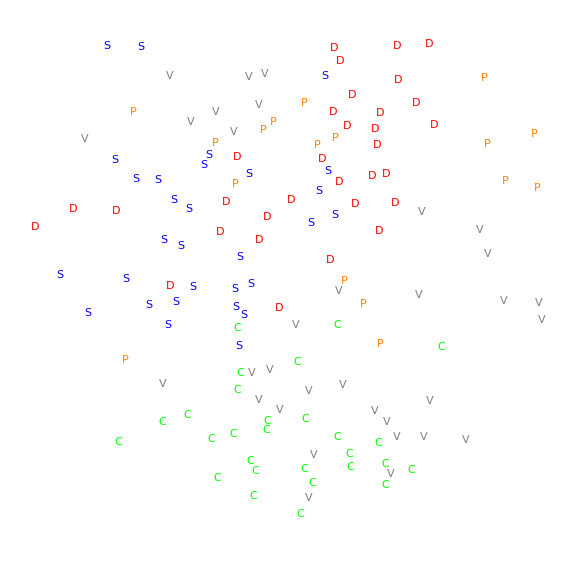

```mathematica
g=FeatureSpacePlot[Keys[trainingset],];
g2=
```

Similar to our first plot it can be seen how artists from the Baroque and the Renaissance are closer together in the plot, while Monet and Van Gogh are mixed together, again due to a similarity in style.

## Search

This code uses the feature extraction tools applied before to generate a function that, in this case, finds the image with the  nearest features. This could be thought of as the shortest distance between two vectors in a multidimensional space.

```mathematica
searchdataset=Keys@trainingset;
nearestf=FeatureNearest[searchdataset]
```

NearestFunction[…]

Again we can apply it to a picture of myself and see the resemblance.

```mathematica
First@nearestf[-Graphics-]
```

-Graphics-

Following the link, you could also upload an image of yourself or even one of your paintings, in the following API deployed to the cloud. You can see what painting from 5 of the most famous painters in history has the nearest features.

```mathematica
CloudDeploy[TestF=FormFunction[{"l"->"Image"},First@nearestf[#l]&]
]
```

CloudObject[https://www.wolframcloud.com/objects/c164eb84-af28-4f0c-adde-4afa387a9f48]

## Further explorations

Recent articles show studies of how machine learning algorithms differentiate between various styles of painting and movements in art history. It is quite interesting to understand how the algorithms differentiate and classify artworks. The tools in the Wolfram Language could be useful for this purpose.

https://arxiv.org/pdf/1801.07729.pdf

https://arxiv.org/abs/1706.07068

## Author contact information

Diego Gutierrez Coronel

06/28/2018

dgutie10@hawk.iit.edu

Special thanks to my mentor Vladimir Grankovsky